# Feature Space

Data features exploration

Pavlo Apisov, Jun. 27,  2018

In the world of machine learning, dimensionality is a serious thing to consider because in some cases the more dimensions in data the harder it could be to learn and generalize.

We can use feature space to control number of dimensions and use data in more meaningful ways.

## Meaningful data

Adding a conceptual meaning to data is the most important quality of a feature space representation.

Exploring a feature space of your data could help to find variables where similar data points closer to each other.

Let’s draw differently colored figures and treat them as our input  data:

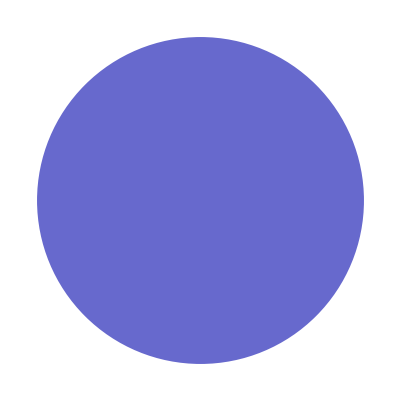
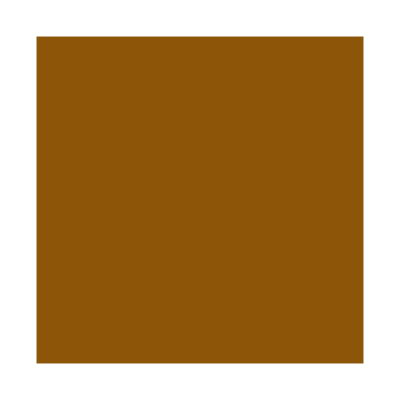
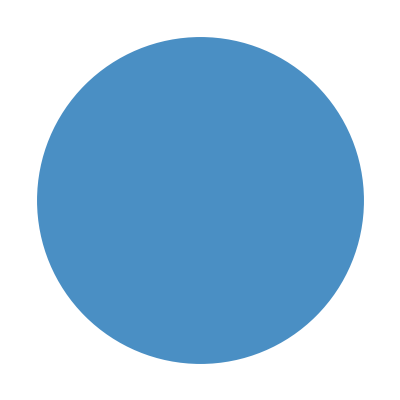
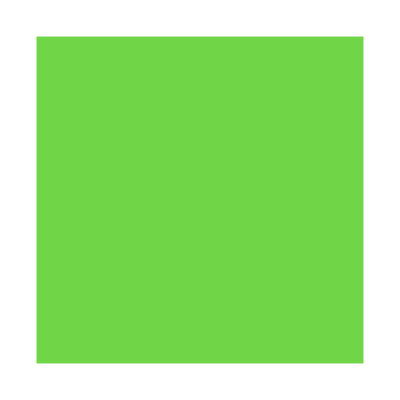
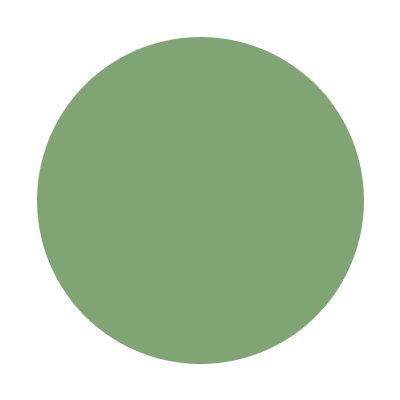
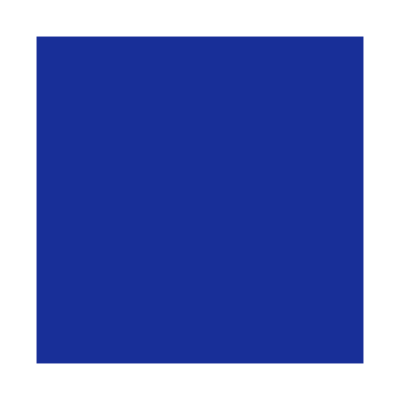
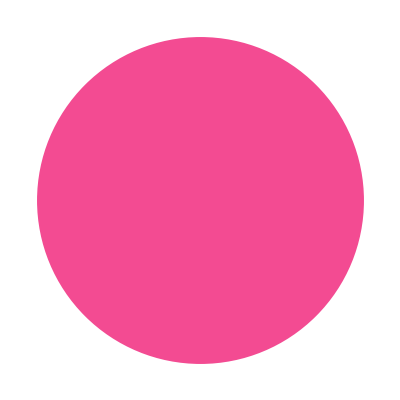
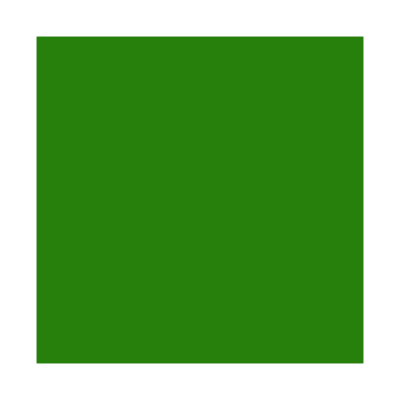

```mathematica
figures = Flatten@Table[{Graphics@{RandomColor[],Disk[]},Graphics@{RandomColor[],Rectangle[]}},5]
```

As an example, in the pixel space, there is no immediate similarity between any of figures above.

If we plot the pixel space of the data we see a layout clustered by color:

```mathematica
FeatureSpacePlot[figures, ImageSize->Small, FeatureExtractor->ImageData]
```

-Graphics-

Nevertheless, if we try to find new features you would want all rectangles to be closer to each other in the new feature space than to any of circles.

To do so, we could use shape of figures as a new feature.

In our case we use edge detection to construct new feature space representation

```mathematica
FeatureSpacePlot[figures, ImageSize->Small, FeatureExtractor-> EdgeDetect]
```

-Graphics-

The way how figures represented in the new feature space is much more reasonable than in the pixel space.

To recapitulate, feature space shows the connections within your data with respect to your task.

I.e for image classification problem, you find features that images with similar meaning(pictures of cat, for example) are closer in that space.

## Exploring handwritten digits

To extend the basic example let’s explore classification of handwritten digits in MNIST dataset.

For the purpose of consistency, we will follow the same steps as in the basic example.

First, show input data(150 random MNIST digits):

```mathematica
digits=Keys[RandomSample[ResourceData["MNIST"],150]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Comparing to the basic example we can find visual similarity in pixel space of digits

We use the same feature plot that extract image data(pixels)

```mathematica
FeatureSpacePlot[digits, FeatureExtractor->ImageData]
```

-Graphics-

As you can notice, even without any specific feature extraction the data is grouped to some level properly.

Thought, since some digits are visually similar(0 and 6 or 7 and 4) we have a lot of mistakes and to solve this problem we need a proper feature extractor.

Our new feature extractor is a pretrained on MNIST data model:

```mathematica
FeatureSpacePlot[digits, FeatureExtractor->NetTake[NetModel["LeNet Trained on MNIST Data"],9]]
```

-Graphics-

From the plot it’s easy to see now how big a role in feature space of a correct feature extractor.

The new feature space has more separated groups of all numbers and  we’ve solved the problem with visually similar being in one cluster.

## Cats and Dogs classification

Now let’s try to do more specific computation and use internal tools of WL to classify images and verify that a correct feature space has a dramatic affect on the classification quality.

Import images of lovely pets:

```mathematica
trainPets = Join[Thread[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-} -> "dog"],Thread[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}->"cat"]
];
```

```mathematica
testPets =Join[
Thread[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}->"cat"],Thread[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}->"dog"]
];
```

As usual, we start with image data as a feature space but in this example we train a model with it rather than just plotting feature space.

Train model using only image data as feature:

```mathematica
imageDataClassificator = Classify[trainPets, FeatureExtractor->ImageData]
```

ClassifierFunction[…]

We use test dataset to measure an accuracy of the trained model:

```mathematica
ClassifierMeasurements[imageDataClassificator, testPets, "Accuracy"]
```

0.555556

Slightly more then 50 % accuracy is not that you want to achieve in any ML task, basically it’s a random guess in a pure form.

How the accuracy will change with the use of a proper feature extractor?

Train model using Automatic WL feature extractor:

```mathematica
automaticClassificator = Classify[trainPets]
```

ClassifierFunction[…]

Repeat the same testing for accuracy as in the case with image data feature space:

```mathematica
ClassifierMeasurements[automaticClassificator, testPets, "Accuracy"]
```

0.861111

Well, this is not the state of the art with nearly 100 % accuracy, however 30 %  improvement is a very good result.

To sum up, feature space is a great tool to explore data and find needed representation that helps to build more accurate ML models.

## Author contact information

Email: apisovp@gmail.com

Twitter: apisov_pavlo

GitHub: apisov